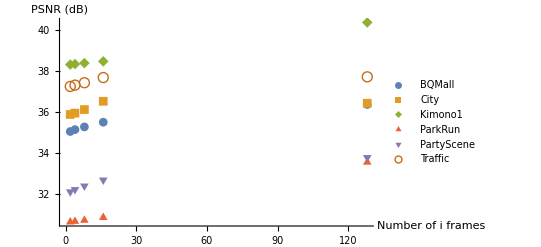

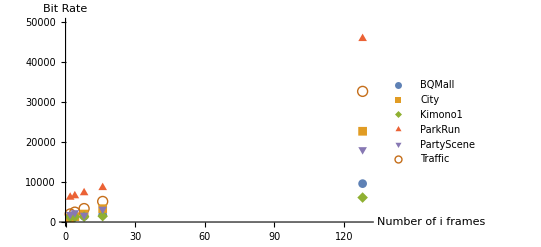

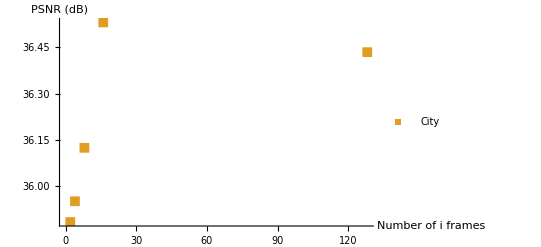

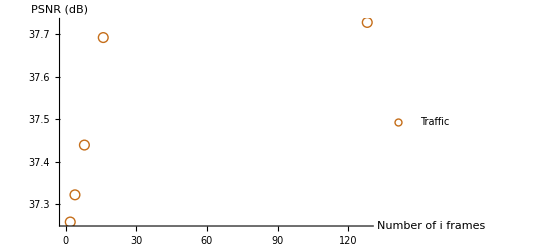

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
NumberOfIFrames = Import["D:/Repos/HEVC_Material/InfoReader/src/result2.txt",{"Data",{2,3,4,5,6},2}];
BQMall_psnr=Import["D:/Repos/HEVC_Material/InfoReader/src/result2.txt",{"Data",{17,18,19,20,21},11}];
BQMallPSNR=Thread[{NumberOfIFrames,{36.3743,35.5063,35.276,35.1444,35.0508}}];
BQMall_bitrate=Import["D:/Repos/HEVC_Material/InfoReader/src/result2.txt",{"Data",{17,18,19,20,21},10}];
BQMallBitRate=Thread[{NumberOfIFrames,{9614.0887,1811.3325,1434.42,1238.3287,1147.4512}}];
City_psnr=Import["D:/Repos/HEVC_Material/InfoReader/src/result2.txt",{"Data",{22,23,24,25,26},11}];
CityPSNR=Thread[{NumberOfIFrames,{36.4345,36.5306,36.1251,35.9523,35.8851}}];
City_bitrate=Import["D:/Repos/HEVC_Material/InfoReader/src/result2.txt",{"Data",{22,23,24,25,26},10}];
CityBitRate=Thread[{NumberOfIFrames,{22733.7712,3338.0062,1994.0437,1351.4588,1036.8075}}];
Kimono1_psnr=Import["D:/Repos/HEVC_Material/InfoReader/src/result2.txt",{"Data",{12,13,14,15,16},11}];
Kimono1PSNR=Thread[{NumberOfIFrames,{40.3909,38.4849,38.3997,38.3527,38.3278}}];
Kimono1_bitrate=Import["D:/Repos/HEVC_Material/InfoReader/src/result2.txt",{"Data",{12,13,14,15,16},10}];
Kimono1BitRate=Thread[{NumberOfIFrames,{6128.7795,1470.2085,1351.869,1293.5475,1265.463}}];
ParkRun_psnr=Import["D:/Repos/HEVC_Material/InfoReader/src/result2.txt",{"Data",{7,8,9,10,11},11}];
ParkRunPSNR=Thread[{NumberOfIFrames,{33.5473,30.8414,30.7035,30.6519,30.6193}}];
ParkRun_bitrate=Import["D:/Repos/HEVC_Material/InfoReader/src/result2.txt",{"Data",{7,8,9,10,11},10}];
ParkRunBitRate=Thread[{NumberOfIFrames,{45955.1375,8615.8031,7320.9656,6562.3375,6202.875}}];
PartyScene_psnr=Import["D:/Repos/HEVC_Material/InfoReader/src/result2.txt",{"Data",{2,3,4,5,6},11}];
PartyScenePSNR=Thread[{NumberOfIFrames,{33.7762,32.674,32.382,32.2088,32.0983}}];
PartyScene_bitrate=Import["D:/Repos/HEVC_Material/InfoReader/src/result2.txt",{"Data",{2,3,6,4,5},10}];
PartySceneBitRate=Thread[{NumberOfIFrames,{18127.8625,3219.0125,1704.9219,2338.,1907.4}}];
Traffic_psnr=Import["D:/Repos/HEVC_Material/InfoReader/src/result2.txt",{"Data",{32,33,34,35,36},11}];
TrafficPSNR=Thread[{NumberOfIFrames,{37.7276,37.692,37.4389,37.3217,37.2577}}];
Traffic_bitrate=Import["D:/Repos/HEVC_Material/InfoReader/src/result2.txt",{"Data",{32,33,34,35,36},10}];
TrafficBitRate=Thread[{NumberOfIFrames,{32728.5056,5151.7125,3364.2881,2474.7825,2012.52}}];
PSNRvsIP=ListPlot[{BQMallPSNR,CityPSNR,Kimono1PSNR,ParkRunPSNR,PartyScenePSNR,TrafficPSNR},PlotMarkers->Automatic,AxesLabel->{"Number of i frames","PSNR (dB)"},PlotLegends->{"BQMall","City","Kimono1","ParkRun","PartyScene","Traffic"}]
Export["D:/Repos/HEVC_Material/InfoReader/src/PSNR_vs_NumberOfIFrames.png",PSNRvsIP,ImageResolution-> 200];
BitRatevsIFrames=ListPlot[{BQMallBitRate,CityBitRate,Kimono1BitRate,ParkRunBitRate,PartySceneBitRate,TrafficBitRate},PlotRange->{{0,130},{0,50000}},PlotMarkers->Automatic,AxesLabel->{"Number of i frames","Bit Rate"},PlotLegends->{"BQMall","City","Kimono1","ParkRun","PartyScene","Traffic"}]
Export["D:/Repos/HEVC_Material/InfoReader/src/BitRate_vs_NumberOfIFrames.png",BitRatevsIFrames,ImageResolution-> 200];
CityPSNRvsIFrames =ListPlot[CityPSNR,PlotMarkers->{■,10},AxesLabel->{"Number of i frames","PSNR (dB)"},PlotLegends->{"City"},PlotStyle->{RGBColor[0.880722,0.611041,0.142051]}]
Export["D:/Repos/HEVC_Material/InfoReader/src/City_PSNR_vs_NumberOfIFrames.png",CityPSNRvsIFrames,ImageResolution-> 200];
TrafficPSNRvsIFrames =ListPlot[TrafficPSNR,PlotMarkers->{○,10},AxesLabel->{"Number of i frames","PSNR (dB)"},PlotLegends->{"Traffic"},PlotStyle->{RGBColor[0.772029,0.431554,0.102387]}]
Export["D:/Repos/HEVC_Material/InfoReader/src/Traffic_PSNR_vs_NumberOfIFrames.png",TrafficPSNRvsIFrames,ImageResolution-> 200];
ColorData[97,"ColorList"]
```